```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (1-loop)

in total: 2 Particles insertions

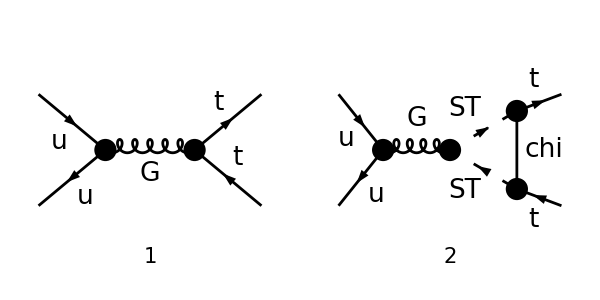

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-1/(p1+p2)^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((GS.GS yDM^2 ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))+2 (φ(-k2)).(γ·q).(φ(k1))) (φ(p1,MT)).(γ·q).(γ̄)^6.(φ(-p2,MT)))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+ⅈ GS (φ(-k2)).γ^Lor2.(φ(k1)) (deltaCTL (φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT))+deltaCTR (φ(p1,MT)).γ^Lor2.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).GS.γ^Lor2.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).GS.γ^Lor2.(γ̄)^7.(φ(-p2,MT))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-1/(p1+p2)^2 ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 GS.GS yDM^2 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+π^2 GS.GS yDM^2 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))) (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))+2 π^2 GS.GS yDM^2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-2 π^2 GS.GS yDM^2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))+GS (φ(-k2)).γ^μ.(φ(k1)) (deltaCTL (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))+deltaCTR (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).GS.γ^μ.(φ(-p2,MT))))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
ampEsimp=FullSimplify[DiracSimplify[ampE//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1}]]
```

-1/(p1+p2)^2 ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (π^2 GS.GS yDM^2 (2 C00 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-MT (φ(-k2)).(γ·p2).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))+(C1+2 C12) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))+MT (φ(-k2)).(γ·p1).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(C1+2 C12) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))))+GS (φ(-k2)).γ^μ.(φ(k1)) (deltaCTL (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT))+deltaCTR (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).GS.γ^μ.(φ(-p2,MT))))

```mathematica
ampEsimp2=FullSimplify[DotSimplify[DiracSimplify[ampEsimp,DiracSubstitute67->True]]//.{GS.GS->GS^2}]
```

-1/(2 (p1+p2)^2)ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 GS yDM^2 (MT (C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+C00 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+(2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+2 π^2 GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+(deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))

```mathematica
sps=Cases2[ampEsimp2,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^5,γ^μ,γ·p1,γ·p2}

```mathematica
(* phi(k1).p1slash.phi(-k2) + phi(k1).p2slash.phi(-k2) = phi(k1).(p1slash+p2slash).phi(-k2) = phi(k1).(k1slash+k2slash).phi(-k2) = 0 *)
ampEsimp3=Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},Simplify]/.{sps[[2]].moms[[3]].sps[[1]]+sps[[2]].moms[[4]].sps[[1]]->0}
```

-1/(2 (p1+p2)^2)ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+2 π^2 C00 GS yDM^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 π^2 GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+(deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[ampEsimp3,DiracSubstitute5->True]/.{GS.GS->GS^2}]
```

-1/(2 (p1+p2)^2)ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) (-(-2 π^2 C00 GS yDM^2+deltaCTL-deltaCTR) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))+(2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))+2 π^2 GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
moms=Cases2[ampEsimp4,DiracGamma]
```

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2}

```mathematica
Collect[ampEsimp4,{sps[[2]].moms[[3]].sps[[1]],sps[[3]].moms[[3]].moms[[1]].sps[[4]],sps[[3]].moms[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[4]].sps[[1]],sps[[2]].moms[[5]].sps[[1]]},FullSimplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))/(2 (p1+p2)^2)+(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))/(2 (p1+p2)^2)+-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT))))/(2 (p1+p2)^2))+-(ⅈ π^2 GS^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2+(ⅈ π^2 GS^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2

```mathematica
DiracSimplify[%]
```

-(ⅈ C1 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ C11 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ C12 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ C1 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ C11 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ C12 MT π^2 yDM^2 GS.GS (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ C00 GS^2 π^2 yDM^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ C00 GS^2 π^2 yDM^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ C00 GS^2 π^2 yDM^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ deltaCTL GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)-(ⅈ deltaCTR GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)-(ⅈ GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ deltaCTL GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)-(ⅈ deltaCTR GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)-(ⅈ deltaCTL GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)+(ⅈ deltaCTR GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) T_Col2Col1^Glu5 T_Col3Col4^Glu5)/(2 (p1+p2)^2)

```mathematica
Collect[%,{sps[[2]].moms[[3]].sps[[1]],sps[[3]].moms[[3]].moms[[1]].sps[[4]],sps[[3]].moms[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[4]].sps[[1]],sps[[2]].moms[[5]].sps[[1]]},Simplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))/(2 (p1+p2)^2)+(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))/(2 (p1+p2)^2)+-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT))))/(2 (p1+p2)^2))+-(ⅈ π^2 GS.GS MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2+(ⅈ π^2 GS.GS MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2

```mathematica
Simplify[DiracGammaCombine[DiracSimplify[%,Expanding->False]]]
```

-1/(2 (p1+p2)^2)ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (-(GS (deltaCTL-deltaCTR)-2 π^2 C00 GS.GS yDM^2) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+2 π^2 GS.GS MT yDM^2 (C11-C12) (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT))+2 π^2 GS.GS MT yDM^2 (C11-C12) (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT))+(2 π^2 C00 GS.GS yDM^2+GS (deltaCTL+deltaCTR)) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 π^2 GS.GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1))-2 π^2 GS.GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1))+2 GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))

```mathematica
DiracSimplify[Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},FullSimplify],Expanding->False,Expand2->False]
```

(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (-2 π^2 C00 GS yDM^2+deltaCTL-deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT)))/(2 (p1+p2)^2)-(ⅈ π^2 GS.GS MT yDM^2 (C11-C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)))/(p1+p2)^2-(ⅈ π^2 GS.GS MT yDM^2 (C11-C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)))/(p1+p2)^2-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(2 (p1+p2)^2)+-(ⅈ π^2 GS.GS MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2+(ⅈ π^2 GS.GS MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2-(ⅈ GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))/(p1+p2)^2

```mathematica
FullSimplify[%]
```

-1/(2 (p1+p2)^2)ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (GS (φ(-k2)).γ^μ.(φ(k1)) ((2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))+2 π^2 GS.GS MT yDM^2 ((C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+(C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))))

```mathematica
DiracGammaCombine[%]
```

-1/(2 (p1+p2)^2)ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (GS (φ(-k2)).γ^μ.(φ(k1)) ((2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))+2 π^2 GS.GS MT yDM^2 ((C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+(C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))))

```mathematica
FullSimplify[%]
```

-1/(2 (p1+p2)^2)ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (GS (φ(-k2)).γ^μ.(φ(k1)) ((2 π^2 C00 GS yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(2 π^2 C00 GS yDM^2+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))+2 π^2 GS.GS MT yDM^2 ((C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+(C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))))

```mathematica
Collect[%,{sps[[3]].moms[[1]].sps[[4]]},Simplify]
```

-(ⅈ π^2 GS.GS MT yDM^2 (C11-C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1))))/(p1+p2)^2-1/(2 (p1+p2)^2)ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (-(GS (deltaCTL-deltaCTR)-2 π^2 C00 GS.GS yDM^2) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(2 π^2 C00 GS.GS yDM^2+GS (deltaCTL+deltaCTR)) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 π^2 GS.GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1))-2 π^2 GS.GS MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1))+2 GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).GS.γ^μ.(φ(-p2,MT)))

### EFT Values (High Mass Limit)

```mathematica
C00eft=Collect[FullSimplify[Expand[(PaXEvaluate[PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))})]/.{s MT^2->0}],{Epsilon,s,Log[ScaleMu^2/mST^2],MT},FullSimplify];
Print["C_00 = ",C00eft];Print["-----------"];
C1eft=Collect[PaXEvaluate[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_1 = ",C1eft];Print["-----------"];
C11eft=Collect[PaXEvaluate[PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_11 = ",C11eft];Print["-----------"];
C12eft=Collect[PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_12 = ",C12eft]
```

C_00 = ((2 mChi^6+3 mST^2 mChi^4-6 mST^2 log(mChi^2/mST^2) mChi^4-6 mST^4 mChi^2+mST^6) MT^2)/(192 (mChi^2-mST^2)^4 π^4)+(-2 log(mChi^2/mST^2) mChi^4+3 mChi^4-4 mST^2 mChi^2+mST^4)/(128 (mChi^2-mST^2)^2 π^4)+(s (6 log(mChi^2/mST^2) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6))/(1152 (mChi^2-mST^2)^4 π^4)+(log(μ^2/mST^2))/(64 π^4)+1/(64 ε π^4)

-----------

C_1 = -(-2 log(mChi^2/mST^2) mChi^4+3 mChi^4-4 mST^2 mChi^2+mST^4)/(64 (mChi^2-mST^2)^3 π^4)

-----------

C_11 = (-6 log(mChi^2/mST^2) mChi^6+11 mChi^6-18 mST^2 mChi^4+9 mST^4 mChi^2-2 mST^6)/(288 (mChi^2-mST^2)^4 π^4)

-----------

C_12 = (-6 log(mChi^2/mST^2) mChi^6+11 mChi^6-18 mST^2 mChi^4+9 mST^4 mChi^2-2 mST^6)/(576 (mChi^2-mST^2)^4 π^4)

```mathematica
A0=Collect[FullSimplify[1/2 Pi^2(C1eft+C11eft+C12eft),Assumptions->{mChi>0,mST>0}],{Epsilon,s},FullSimplify]
```

(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(384 π^2 (mChi^2-mST^2)^4)

```mathematica
B0=SeriesCoefficient[-2/3 C00eft,{s,0,1}]
```

-(18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6)/(1728 π^4 (mChi^2-mST^2)^4)